```mathematica
f1[n_, k_, b_] := Sum[ (-1)^j Binomial[k,j] b^j f[n b^-j],{j,0,Log[b,n]}]
f2[n_, k_, b_] := Sum[ Binomial[k+j-1, k-1] b^j f1[ n b^-j,k,b],{j,0,Log[b,n]}]
```

```mathematica
f[n_] :=If[Mod[n,8]<4, 1,0]
```

```mathematica
f1[10,I,1.01]
```

14.3143-2.42347 ⅈ

```mathematica
f1[15,1/2,2]
```

-45/16

```mathematica
FullSimplify[f2[100,I,1.1]]
```

-0.506366-9.32587×10^-15 ⅈ

```mathematica
f3[n_, k_, b_] := DiscretePlot[ (-1)^j Binomial[k,j] b^j f[n/b^j],{j,0,Log[b,n]}]
f4[n_,k_,b_]:=DiscretePlot[ Binomial[k+j-1, k-1] b^j f1[ n/b^j,k,b],{j,0,Log[b,n]}]
```

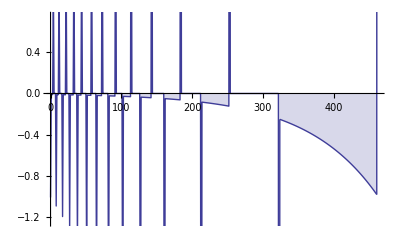

```mathematica
f4[100,1,1.01]
```

```mathematica
f1a[n_, k_, b_] := Sum[ Binomial[k,j] b^j f[n/b^j],{j,0,Log[b,n]}]
f2a[n_, k_, b_] := Sum[ (-1)^j Binomial[k+j-1, k-1] b^j f1a[ n/b^j,k,b],{j,0,Log[b,n]}]
```

```mathematica
f2a[10,2,2]
```

10

```mathematica
f4a[n_,k_,b_]:=DiscretePlot[ (-1)^j Binomial[k+j-1, k-1] b^j f1a[ n/b^j,k,b],{j,0,Log[b,n]}]
```

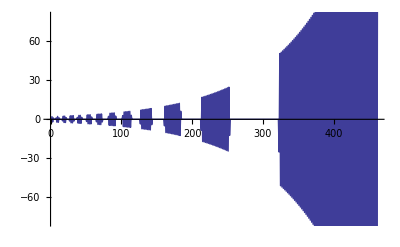

```mathematica
f4a[100,1,1.01]
```

```mathematica
f1b[n_, k_, b_] := Sum[ (-1)^j Binomial[k,j] f[n/b^j],{j,0,Log[b,n]}]
f2b[n_, k_, b_] := Sum[ Binomial[k+j-1, k-1]  f1b[ n/b^j,k,b],{j,0,Log[b,n]}]
```

```mathematica
f2b[10,2,2]
```

10

```mathematica
f4b[n_,k_,b_]:=DiscretePlot[ Binomial[k+j-1, k-1] f1b[ n/b^j,k,b],{j,0,Log[b,n]}]
```

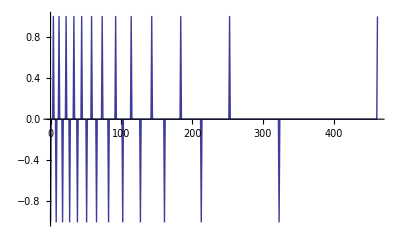

```mathematica
f4b[100,1,1.01]
```

```mathematica
f4b2[n_,k_,b_]:=Table[ Binomial[k+j-1, k-1] f1b[ n/b^j,k,b],{j,0,Log[b,n]}]
```

```mathematica
f4b2[10,2,1.01]//TableForm
```

0
0
0
0
0
0
0
0
0
-10
11
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
-92
93
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
-231
232

```mathematica
f4a2[n_,k_,b_]:=Table[ Binomial[k+j-1, k-1] b^j f1[ n/b^j,k,b],{j,0,Log[b,n]}]//TableForm
```

```mathematica
f4a2[10,2,1.01]//TableForm
```

-2.0008
-0.001616
-0.00244824
-0.00329696
-0.00416242
-0.00504485
-0.00594451
-0.00686167
-0.00779657
-0.00874948
-0.00972067
-0.0107104
-0.011719
-0.0127466
-0.0137937
-0.0148604
-0.0159471
-0.017054
-0.0181814
-0.0193297
-0.0204992
55.2935
-57.2741
-0.0181031
-0.019046
-0.0200059
-0.0209832
-0.0219779
-0.0229905
-0.0240211
-0.02507
-0.0261375
-0.0272238
-0.0283293
-0.0294541
-0.0305986
-0.0317631
-0.0329477
-0.0341529
-0.0353789
-0.036626
-0.0378946
-0.0391848
-0.040497
-0.0418316
-0.0431888
-0.0445689
-0.0459724
-0.0473994
-0.0488505
171.074
-172.787
-0.035567
-0.0366005
-0.037651
-0.038719
-0.0398045
-0.0409078
-0.0420293
-0.043169
-0.0443274
-0.0455046
-0.046701
-0.0479167
-0.049152
-0.0504073
-0.0516827
-0.0529787
-0.0542953
-0.055633
-0.0569921
-0.0583727
-0.0597753
-0.0612001
-0.0626474
-0.0641175
-0.0656108
-0.0671275
-0.068668
-0.0702326
-0.0718216
-0.0734353
-0.0750742
-0.0767385
-0.0784286
-0.0801448
-0.0818875
-0.083657
-0.0854537
-0.087278
-0.0891302
464.109
-464.647
-0.0474292
-0.0484131
-0.0494119
-0.0504259
-0.0514552
-0.0525001
-0.0535607
-0.0546372
-0.05573
-0.0568391
-0.0579649
-0.0591074
-0.0602671
-0.061444
-0.0626384
-0.0638506
-0.0650807
-0.0663291
-0.0675959
-0.0688815
-0.0701859
-0.0715096
-0.0728528
-0.0742156
-0.0755984
-0.0770015
-0.078425
-0.0798694
-0.0813347
-0.0828214
-0.0843297
-0.0858599
-0.0874122
-0.0889871
-0.0905846
-0.0922052
-0.0938492
-0.0955168
-0.0972084
-0.0989243
-0.100665
-0.10243
-0.104221
-0.106037
-0.107879
-0.109747
-0.111642
-0.113564
-0.115513
-0.11749
-0.119495
-0.121528
-0.12359
-0.125681
-0.127801
-0.129951
-0.132131
-0.134342
-0.136584
-0.138858
-0.141163
-0.1435
-0.145871
-0.148274
-0.15071
-0.153181
-0.155686
1613.9
-1608.
0.
0.
0.
0.
0.
0.
-1.99672×10^-13
0.
-2.06096×10^-13
0.
-2.12698×10^-13
0.
0.
0.
-2.26452×10^-13
-2.30008×10^-13
0.
-2.37268×10^-13
0.
0.
0.
0.
0.
0.
-2.64276×10^-13
-2.68346×10^-13
0.
-2.76652×10^-13
-2.80889×10^-13
0.
0.
0.
0.
0.
0.
-3.12188×10^-13
0.
-3.2168×10^-13
0.
-3.31427×10^-13
0.
0.
-3.46541×10^-13
0.
-3.56955×10^-13
-3.62266×10^-13
0.
0.
0.
-3.84225×10^-13
-3.89898×10^-13
-3.95646×10^-13
0.
0.
0.
0.
-4.25543×10^-13
0.
0.
0.
-4.5091×10^-13
0.
0.
0.
0.
0.
-4.91529×10^-13
-9.97224×10^-13
-2310.
2320.